Function: 100 ⅇ^(-77 x_^2)

Сoefficients: σ=50 (1+x_)^2 μ=1. β=1925 x_

Mathematica Solution of the Boundary Value Problem:

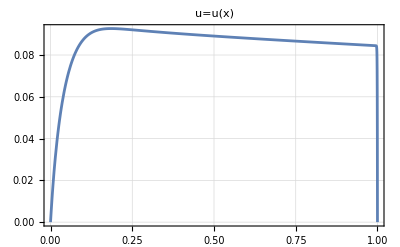

###############         Step = 1   n = 5      #################

Calculation  of the Finite Element Equations:

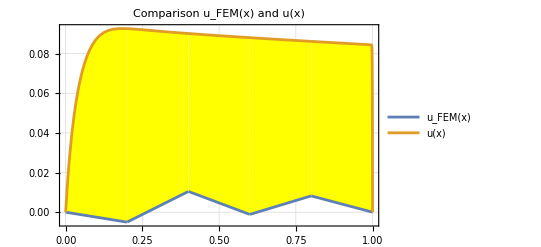

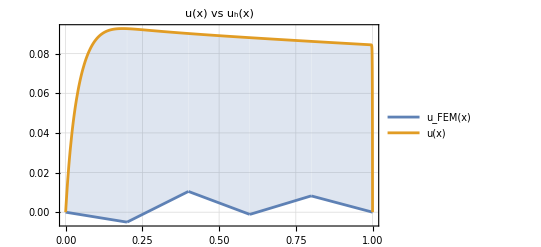
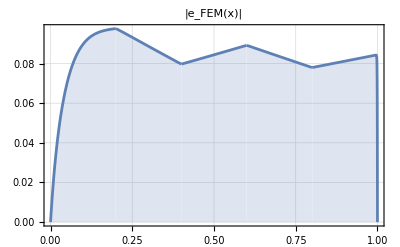
Finite Element Approximation for n = 5 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 2   n = 10      #################

Calculation  of the Finite Element Equations:

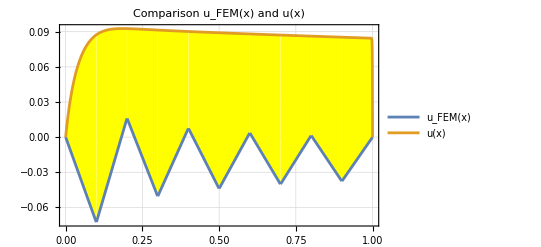

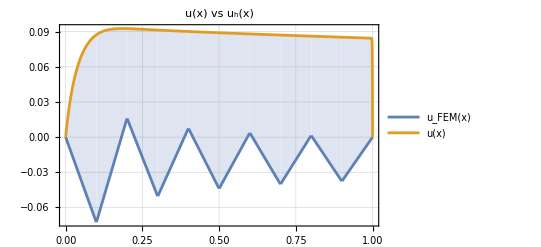
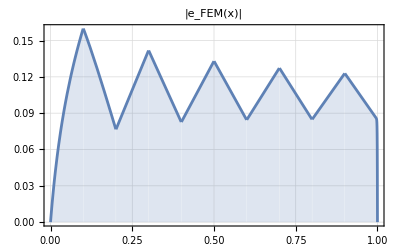
Finite Element Approximation for n = 10 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 3   n = 20      #################

Calculation  of the Finite Element Equations:

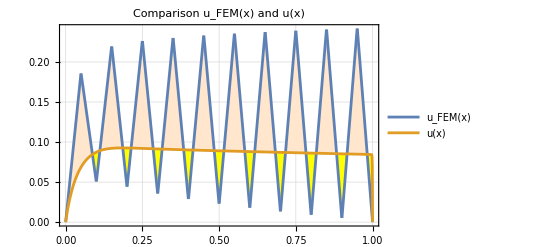

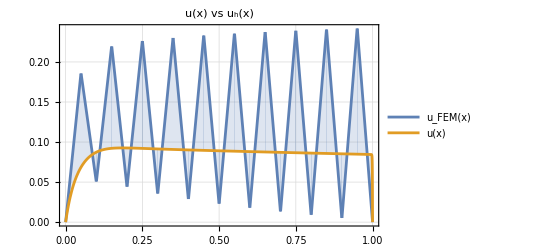
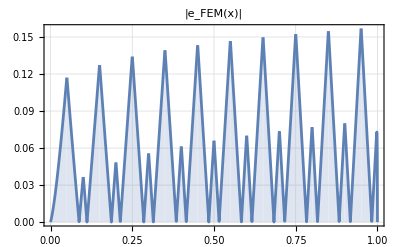
Finite Element Approximation for n = 20 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 4   n = 40      #################

Calculation  of the Finite Element Equations:

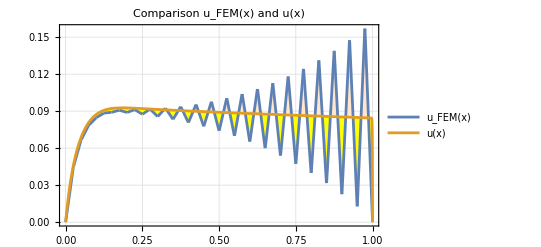

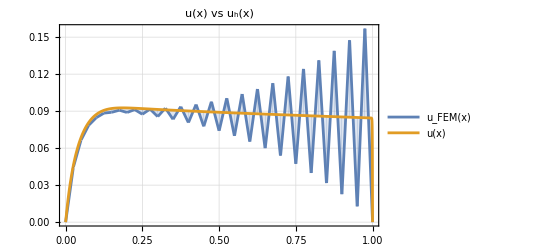
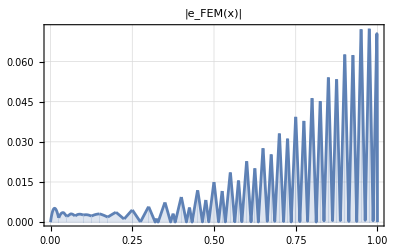
Finite Element Approximation for n = 40 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 5   n = 80      #################

Calculation  of the Finite Element Equations:

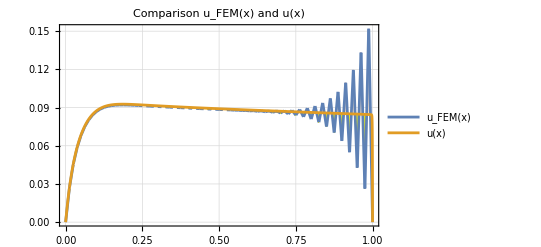

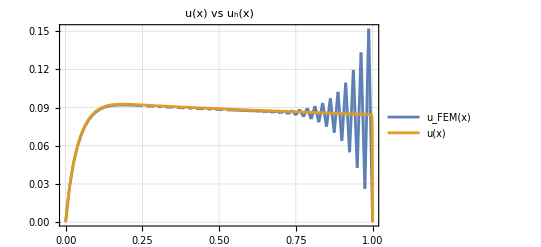
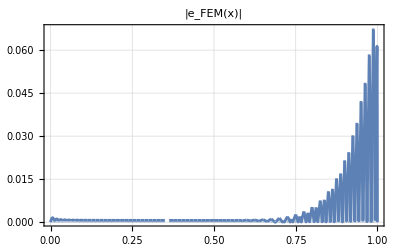
Finite Element Approximation for n = 80 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 6   n = 159      #################

Calculation  of the Finite Element Equations:

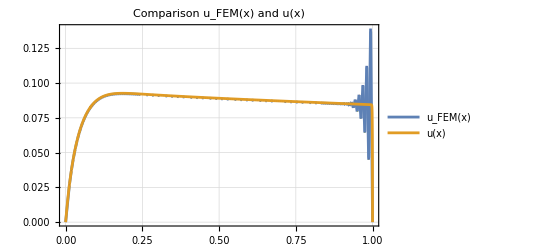

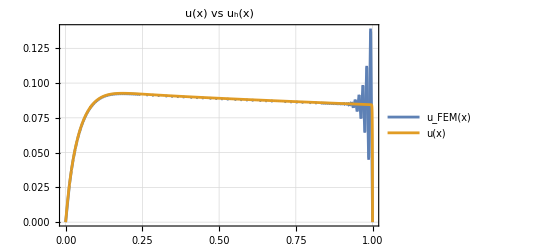
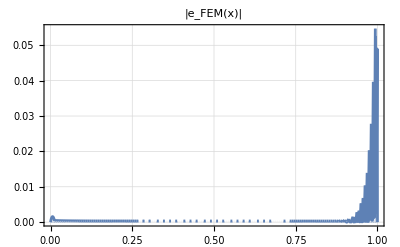
Finite Element Approximation for n = 159 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 7   n = 177      #################

Calculation  of the Finite Element Equations:

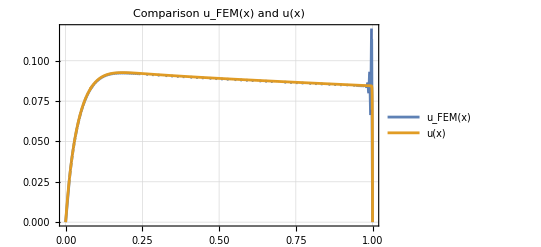

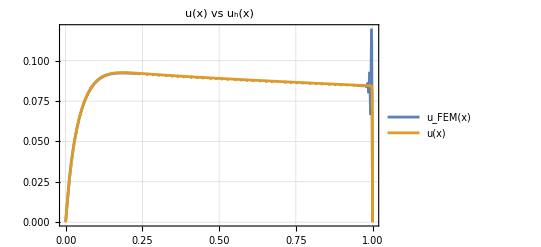
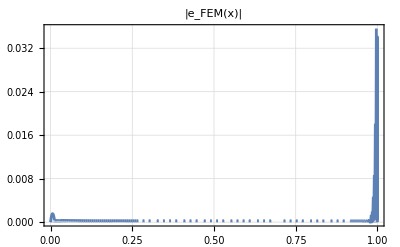
Finite Element Approximation for n = 177 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 8   n = 188      #################

Calculation  of the Finite Element Equations:

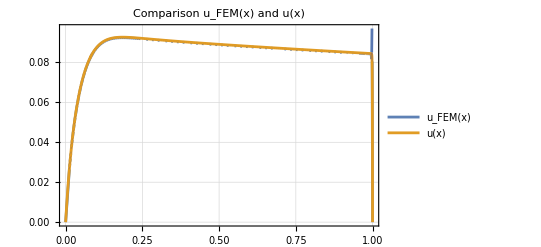

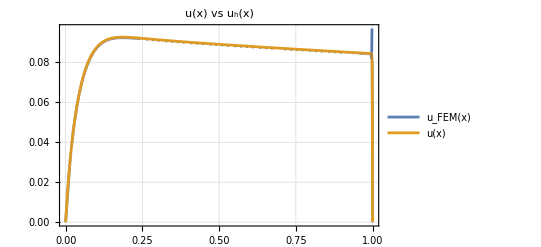
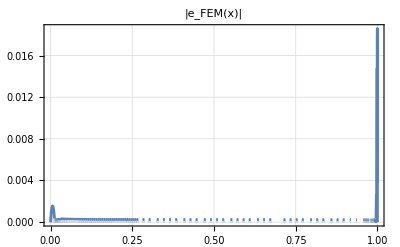
Finite Element Approximation for n = 188 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 9   n = 197      #################

Calculation  of the Finite Element Equations:

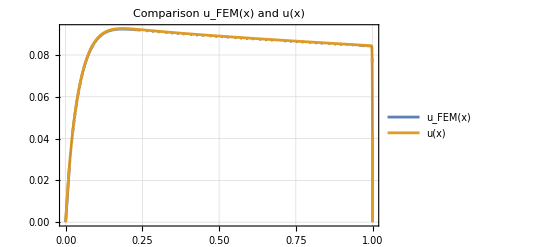

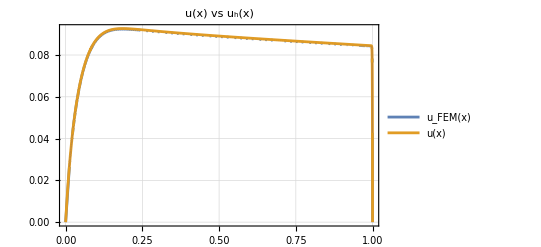
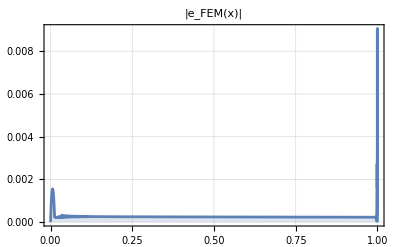
Finite Element Approximation for n = 197 :  -Graphics-   *****  and Its Error     -Graphics-    *****

###############         Step = 10   n = 211      #################

Calculation  of the Finite Element Equations:

```mathematica
operator=-μ[x]v''[x]+(β[x]-μ'[x])v'[x]+σ[x]v[x];

f[x_]:=100Exp[-77*x^2];
σ[x_]:=50*(1+x)^2;
μ[x_]:=1.;
β[x_]:=1925*x;
a=0;b=1;


(*f[x_]:=500Exp[-200.0*x^2];
σ[x_]:=0;
μ[x_]:=1.;
β[x_]:=-100*x;
(*a=0;*)b=1;
a=-1;*)

(*f[x_]:=100;
σ[x_]:=100;
μ[x_]:=0.1;
β[x_]:=0;
a=0;b=1;*)

(*f[x_]:=100;
σ[x_]:=100;
μ[x_]:=1.;
β[x_]:=0;
a=0;b=1;*)

Print ["Function: ",f[x_]];
Print["Сoefficients: σ=",σ[x_]," μ=",μ[x_]," β=",β[x_]];
Print["Mathematica Solution of the Boundary Value Problem:"];
u=NDSolveValue[{operator==f[x],v[a]==0,v[b]==0},v,{x,a,b}];


Print[figExact=Plot[u[x],{x,a,b},Frame->True,GridLines->Automatic,PlotLabel->" u=u(x)",PlotRange->Full]];

(*Basic Functions and Finite Element Approximation*)
Subscript[u, FEM][x_]:=∑_(k=1)^(n-1) r⟦k⟧Subscript[ψ, k][x];
Subscript[e, FEM][x_]:=u[x]-Subscript[u, FEM][x];

η[i_,x_]:=Piecewise[{{(s⟦i+1⟧-x)/(s⟦i+1⟧-s⟦i⟧),s⟦i⟧ ≤x≤s⟦i+1⟧},{0,x≤s⟦i⟧&&x≥s⟦i+1⟧}}];
ρ[i_,x_]:=Piecewise[{{(x-s⟦i⟧)/(s⟦i+1⟧-s⟦i⟧),s⟦i⟧ ≤x≤s⟦i+1⟧},{0,x≤s⟦i⟧&&x≥s⟦i+1⟧}}];
Subscript[ψ, i_][x_]:=If[i==0,η[1,x],If[i==n,ρ[n,x],Piecewise[{{ρ[i,x],s⟦i⟧ ≤x≤s⟦i+1⟧},{η[i+1,x],s⟦i+1⟧ ≤x≤s⟦i+2⟧}}]]];
tableFEM={{}};titleFEM={"step","n","‖u_FEM‖_0","|u_FEM|_1","‖u_FEM‖_1","u_FEM(x) vs u(x)","‖e_FEM‖_0","‖e_FEM‖_1","ε_FEM"};
step=1;
n=5;
Subscript[check, δ]=False;
tol=0.5;
hFEM=(b-a)/n;
s=Table[a+i*hFEM,{i,0,n}];
While [Subscript[check, δ]==False,


Print[" ###############         Step = ",step,"   n = ",n,"      #################"];

Print["Calculation  of the Finite Element Equations:"];matrixFEM=SparseArray[{i_,j_}/;Abs[i-j]≤1:>NIntegrate[μ[x]Subscript[ψ, i]'[x]Subscript[ψ, j]'[x]+(β[x]Subscript[ψ, j]'[x]+σ[x]Subscript[ψ, j][x])Subscript[ψ, i][x],{x,a,b},Method->"DoubleExponential"],{n-1,n-1}];fsideFEM=Table[NIntegrate[f[x]Subscript[ψ, i][x],{x,a,b}],{i,1,n-1}];
r=LinearSolve[matrixFEM,fsideFEM];(*System of Finite Element Equations and  its Solution*)
Subscript[ε, FEM]=0;
For [i=1, i<=n, i=i+1,
Subscript[x, av]=(s⟦i⟧+s⟦i+1⟧)/2;

Pe=(hFEM β[Subscript[x, av]])/μ[Subscript[x, av]];
Sh=(hFEM^2*σ[Subscript[x, av]])/μ[Subscript[x, av]];

Subscript[ε, i]=hFEM^3/μ[Subscript[x, av]]*(f[Subscript[x, av]]-β[Subscript[x, av]]D[Subscript[u, FEM][Subscript[x, av]], x]-σ[Subscript[x, av]]*Subscript[u, FEM][Subscript[x, av]])^2/(10+Pe*Sh);
Subscript[ε, FEM]=Subscript[ε, FEM]+Subscript[ε, i];

];
Subscript[ε, FEM]=5/6 Subscript[ε, FEM];
Subscript[δ, FEM]=Table[RealAbs[(Subscript[e, FEM][s⟦i⟧])/(Subscript[u, FEM][s⟦i⟧]+Subscript[ε, FEM])*100],{i,1,n+1}];
figureFEM=Plot[{Subscript[u, FEM][x],u[x]},{x,a,b},Frame->True,GridLines->Automatic,Filling->{1->{{2},{Yellow,LightOrange}}},PlotRange->Full,PlotLegends->"Expressions",PlotLabel->":0421omparison u_FEM(x) and u(x)"];Print[figureFEM];figErrorFEM=Plot[Abs[Subscript[e, FEM][x]],{x,a,b},Frame->True,GridLines->Automatic,PlotLabel->" |e_FEM(x)|",PlotRange->Full,Filling->Bottom];figFEM=Plot[{Subscript[u, FEM][x],u[x]},{x,a,b},Frame->True,GridLines->Automatic,PlotLabel->" u(x) vs u_h(x)",PlotRange->Full,Filling->{1->{2}},PlotLegends->"Expressions"];
$MaxPiecewiseCases=1000;
Print["Finite Element Approximation for n = ",n," :  ",figFEM,"   *****  and Its Error     ",figErrorFEM,"    *****     "];
normFEM0=√NIntegrate[Subscript[u, FEM][x]^2,{x,a,b}];seminormFEM1=√NIntegrate[Subscript[u, FEM]'[x]^2,{x,a,b}];normFEM1=√NIntegrate[Subscript[u, FEM][x]^2+Subscript[u, FEM]'[x]^2,{x,a,b}];normErrFEM0=√NIntegrate[Subscript[e, FEM][x]^2,{x,a,b}];seminormErr1=√NIntegrate[Subscript[e, FEM]'[x]^2,{x,a,b}];normErrFEM1=√NIntegrate[Subscript[e, FEM][x]^2+Subscript[e, FEM]'[x]^2,{x,a,b}];
estimatorErr1=√NIntegrate[Subscript[ε, FEM],{x,a,b}];
stringFEM={step,n,normFEM0,seminormFEM1,normFEM1,figFEM,normErrFEM0,normErrFEM1, estimatorErr1};
tableFEM=AppendTo[tableFEM,stringFEM];
Subscript[n, temp]=n;
Subscript[s, temp]={s⟦1⟧};
Subscript[check, δ]=True;
For [i=1, i<=n, i=i+1,
If[(Subscript[δ, FEM]⟦i+1⟧+Subscript[δ, FEM]⟦i⟧)/2<tol,
AppendTo[Subscript[s, temp],s⟦i+1⟧],

(
Subscript[s, next]=(s⟦i⟧+s⟦i+1⟧)/2;
AppendTo[Subscript[s, temp],Subscript[s, next]];
AppendTo[Subscript[s, temp],s⟦i+1⟧];
Subscript[n, temp]++;
Subscript[check, δ]=False;
)
];
];
n=Subscript[n, temp];
s=Subscript[s, temp];
hFEM=(b-a)/n;
step++;
];

tableFEM=AppendTo[tableFEM,titleFEM];tableFEM=Prepend[tableFEM,titleFEM];tableFEM=Delete[tableFEM,{2}];Print["Convergence of the Finite Element Approximations:"];Print["   *****  *****     *****  *****    "];
Grid[tableFEM,Frame->All]
(*Clear[n,step,matRG]*)normu0=√NIntegrate[u[x]^2,{x,a,b}];seminormu1=√NIntegrate[u'[x]^2,{x,a,b}];normu1=√NIntegrate[u[x]^2+u'[x]^2,{x,a,b}];Print["‖u‖_0 = ",normu0,"     ","|u|_1 = ",seminormu1,"     ","‖u‖_1 = ",normu1];
```